# Data Analysis: Autosomal

## Data Pre - Processing

Load

Setup folders, and return CSV filenames in the experiments sub-folder.

```mathematica
SetDirectory["/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/ProcessedData"];
experimentsFolder="/Autosomal/";
fileNames=FileNames["*.csv",Directory[]<>experimentsFolder];
```

Import the data from the files, flatten it into a large dataset, and store the headers.

```mathematica
header=Import[fileNames[[1]]][[1]];
rawData=(Import[#][[2;;All]])&/@fileNames;
flattenedData=ToExpression/@Flatten[rawData,1];
```

Show summaries.

```mathematica
{header,Range[header//Length]}//Transpose//Grid[#,Frame->All]&
experimentsIDVectors=Cases[flattenedData,{homing_,femaleDep_,hFitness_,bFitness_,___}->{homing,femaleDep,hFitness,bFitness}];
Grid[{
header[[1;;4]],
(experimentsIDVectors[[All,#]]//DeleteDuplicates//Sort)&/@Range[4]
}//Transpose,Frame->All
]
```

Homing | 1
FemaleDeposition | 2
HFitness | 3
BFitness | 4
Day | 5
H | 6
W | 7
R | 8
B | 9

Homing | {0.65,0.7,0.75,0.8,0.9,0.95,0.99}
FemaleDeposition | {0.,0.25,0.5,0.75}
HFitness | {0.,0.02,0.04,0.06,0.08,0.1}
BFitness | {0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4}

Pre - Process

Calculate the "max" number of days, and pop sizes in case these are useful for sampling and re-scaling the output.

```mathematica
maxDay=flattenedData[[All,5]]//Max;
maxTotalPop=Max[Total/@flattenedData[[All,6;;9]]];
maxAllelePop=Max[Max/@flattenedData[[All,6;;9]]];
```

```mathematica
reShapedData={
#[[1]],#[[2]],#[[3]],#[[4]],
#[[5]]//Round,
#[[6]]/maxTotalPop,
#[[7]]/maxTotalPop,
#[[8]]/maxTotalPop,
#[[9]]/maxTotalPop
}&/@flattenedData;
```

```mathematica
dayProbed=999;
probedData=Cases[reShapedData,{homing_,femaleDep_,hFitness_,bFitness_,dayProbed,h_,w_,r_,b_}->{homing,femaleDep,hFitness,bFitness,h/(h+w+r+b)}];
```

## Analyze

Reshape into I/O

```mathematica
outInDataForm=(#[[5]]->{#[[1]],#[[2]],#[[3]],#[[4]]})&/@probedData;
inOutDataForm=({#[[1]],#[[2]],#[[3]],#[[4]]}->#[[5]])&/@probedData;
```

Find Clusters (Exploratory)

```mathematica
clusters=FindClusters[inOutDataForm];
Length[clusters]
```

7

{{0.65,0.,0.,0.25,0.915922},{0.65,0.,0.,0.3,0.896274},{0.65,0.,0.,0.35,0.924923},{0.65,0.,0.,0.4,0.914792},{0.65,0.,0.02,0.3,0.897491},{0.65,0.,0.02,0.35,0.893245},{0.65,0.,0.02,0.4,0.897337},{0.65,0.25,0.,0.2,0.876609},{0.65,0.25,0.,0.25,0.898927},{0.65,0.25,0.,0.3,0.902084},{0.65,0.25,0.,0.35,0.895794},{0.65,0.25,0.,0.4,0.914078},{0.65,0.25,0.02,0.2,0.837223},{0.65,0.25,0.02,0.25,0.847157},{0.65,0.25,0.02,0.3,0.869624},{0.65,0.25,0.02,0.35,0.877571},{0.65,0.25,0.02,0.4,0.862945},{0.65,0.25,0.04,0.25,0.817052},{0.65,0.25,0.04,0.3,0.821182},{0.65,0.5,0.,0.25,0.832259},{0.65,0.5,0.,0.3,0.858647},{0.65,0.5,0.,0.35,0.875602},{0.65,0.5,0.,0.4,0.873767},{0.65,0.5,0.02,0.25,0.808292},{0.65,0.5,0.02,0.3,0.802286},{0.65,0.5,0.02,0.35,0.815642},{0.65,0.5,0.02,0.4,0.826817},{0.65,0.5,0.04,0.25,0.703269},{0.65,0.75,0.,0.3,0.755097},{0.65,0.75,0.,0.35,0.698684},{0.65,0.75,0.,0.4,0.734365},{0.65,0.75,0.02,0.3,0.644029},{0.65,0.75,0.02,0.35,0.679583},{0.65,0.75,0.02,0.4,0.642563},{0.7,0.,0.,0.25,0.941304},{0.7,0.,0.,0.3,0.940289},{0.7,0.,0.,0.35,0.936698},{0.7,0.,0.,0.4,0.932209},{0.7,0.,0.02,0.3,0.915638},{0.7,0.,0.02,0.35,0.91932},{0.7,0.,0.02,0.4,0.918365},{0.7,0.25,0.,0.2,0.900835},{0.7,0.25,0.,0.25,0.90628},{0.7,0.25,0.,0.3,0.926781},{0.7,0.25,0.,0.35,0.919504},{0.7,0.25,0.,0.4,0.924555},{0.7,0.25,0.02,0.2,0.854539},{0.7,0.25,0.02,0.25,0.893743},{0.7,0.25,0.02,0.3,0.882903},{0.7,0.25,0.02,0.35,0.897545},{0.7,0.25,0.02,0.4,0.864781},{0.7,0.25,0.04,0.25,0.845739},{0.7,0.25,0.04,0.3,0.802024},{0.7,0.5,0.,0.25,0.884834},{0.7,0.5,0.,0.3,0.886152},{0.7,0.5,0.,0.35,0.892938},{0.7,0.5,0.,0.4,0.893428},{0.7,0.5,0.02,0.25,0.848919},{0.7,0.5,0.02,0.3,0.830223},{0.7,0.5,0.02,0.35,0.862329},{0.7,0.5,0.02,0.4,0.85602},{0.7,0.5,0.04,0.25,0.771379},{0.7,0.75,0.,0.3,0.795682},{0.7,0.75,0.,0.35,0.785429},{0.7,0.75,0.,0.4,0.835917},{0.7,0.75,0.02,0.3,0.736301},{0.7,0.75,0.02,0.35,0.686537},{0.7,0.75,0.02,0.4,0.678632},{0.75,0.,0.,0.25,0.946806},{0.75,0.,0.,0.3,0.949709},{0.75,0.,0.,0.35,0.949244},{0.75,0.,0.,0.4,0.945909},{0.75,0.,0.02,0.3,0.927184},{0.75,0.,0.02,0.35,0.937315},{0.75,0.,0.02,0.4,0.928574},{0.75,0.25,0.,0.2,0.91639},{0.75,0.25,0.,0.25,0.931535},{0.75,0.25,0.,0.3,0.911951},{0.75,0.25,0.,0.35,0.931844},{0.75,0.25,0.,0.4,0.939449},{0.75,0.25,0.02,0.2,0.893857},{0.75,0.25,0.02,0.25,0.904033},{0.75,0.25,0.02,0.3,0.910112},{0.75,0.25,0.02,0.35,0.916922},{0.75,0.25,0.02,0.4,0.926936},{0.75,0.25,0.04,0.25,0.882426},{0.75,0.25,0.04,0.3,0.883283},{0.75,0.5,0.,0.25,0.882585},{0.75,0.5,0.,0.3,0.923777},{0.75,0.5,0.,0.35,0.890245},{0.75,0.5,0.,0.4,0.909385},{0.75,0.5,0.02,0.25,0.868121},{0.75,0.5,0.02,0.3,0.855404},{0.75,0.5,0.02,0.35,0.874138},{0.75,0.5,0.02,0.4,0.90159},{0.75,0.5,0.04,0.25,0.845549},{0.75,0.75,0.,0.3,0.816079},{0.75,0.75,0.,0.35,0.79066},{0.75,0.75,0.,0.4,0.83517},{0.75,0.75,0.02,0.3,0.764192},{0.75,0.75,0.02,0.35,0.769426},{0.75,0.75,0.02,0.4,0.77117},{0.8,0.,0.,0.25,0.952956},{0.8,0.,0.,0.3,0.961259},{0.8,0.,0.,0.35,0.966187},{0.8,0.,0.,0.4,0.964463},{0.8,0.,0.02,0.3,0.943497},{0.8,0.,0.02,0.35,0.95351},{0.8,0.,0.02,0.4,0.960705},{0.8,0.25,0.,0.2,0.934597},{0.8,0.25,0.,0.25,0.942131},{0.8,0.25,0.,0.3,0.947327},{0.8,0.25,0.,0.35,0.956409},{0.8,0.25,0.,0.4,0.953657},{0.8,0.25,0.02,0.2,0.914071},{0.8,0.25,0.02,0.25,0.929481},{0.8,0.25,0.02,0.3,0.924416},{0.8,0.25,0.02,0.35,0.925792},{0.8,0.25,0.02,0.4,0.939547},{0.8,0.25,0.04,0.3,0.907953},{0.8,0.5,0.,0.25,0.919881},{0.8,0.5,0.,0.3,0.907935},{0.8,0.5,0.,0.35,0.941051},{0.8,0.5,0.,0.4,0.912089},{0.8,0.5,0.02,0.25,0.890562},{0.8,0.5,0.02,0.3,0.869723},{0.8,0.5,0.02,0.35,0.900213},{0.8,0.5,0.02,0.4,0.908066},{0.8,0.75,0.,0.3,0.857568},{0.8,0.75,0.,0.35,0.870773},{0.8,0.75,0.,0.4,0.895196},{0.8,0.75,0.02,0.3,0.789247},{0.8,0.75,0.02,0.35,0.760134},{0.8,0.75,0.02,0.4,0.796257}}

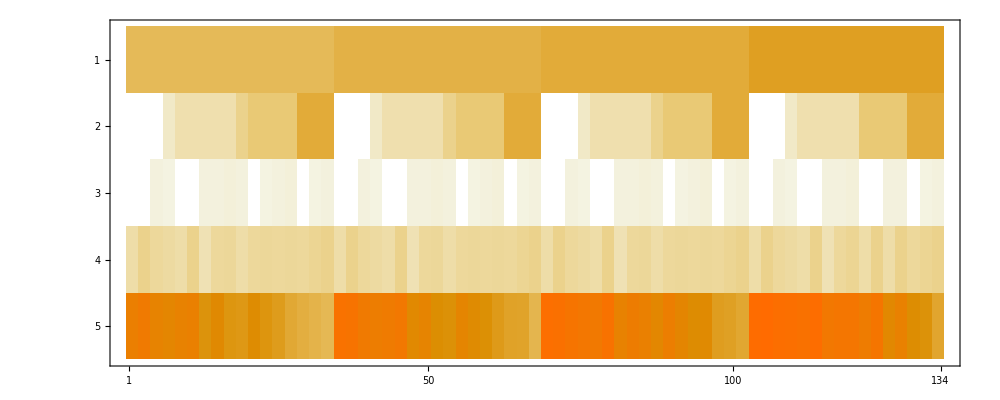

```mathematica
clusterToInspect=2;
clusteredData=Flatten[Cases[outInDataForm,(#->a_)->{a,#}]&/@clusters[[clusterToInspect]],1];
Flatten/@clusteredData
MatrixPlot[%//Transpose,ImageSize->1000]
```

Machine Learning (Predictive)

## One - Fold

Setting up training and validation sets

```mathematica
validationFraction=.9;
samplesNumber=(inOutDataForm//Length);
trainingIndex=samplesNumber*validationFraction//Round;

sample=RandomSample[inOutDataForm];
training=sample[[1;;trainingIndex]];
validation=sample[[(trainingIndex+1);;samplesNumber]];
```

Training and testing

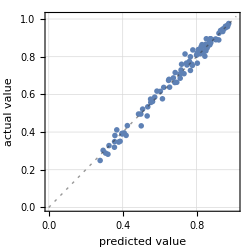
Predictor information
Input type | NumericalVector (length: 4)
Method | GradientBoostedTrees
Standard deviation | 0.0367 ± 0.0074
Loss | 0 ± 0.16
Single evaluation time | 3.37 ms/example
Batch evaluation speed | 48.5 examples/ms
Predictor memory | 642. kB
Training examples used | 864 examples
Training time | 8.81 s
 |  | Predictor Measurements
Number of test examples | 96
Standard deviation | 0.0237 ± 0.002
Standard deviation baseline | 0.205 ± 0.012
Mean cross entropy | -2. ± 0.22
Single evaluation time | 3.08 ms/example
Batch evaluation speed | 2.26 examples/ms
-Graphics- |

```mathematica
predictionFunction=Predict[training
,ValidationSet->validation
,PerformanceGoal->"Quality"
,Method->"GradientBoostedTrees"
];
Grid[{{
PredictorInformation[predictionFunction],
PredictorMeasurements[predictionFunction,validation, "Report"]
}}]
```

## Repeated random sub-sampling validation

```mathematica
{trainingFraction,folds}={.90,10};
samplesNumber=(inOutDataForm//Length);
trainingIndex=(samplesNumber*trainingFraction)//Round;
trainPlots=Table[
(*Pull a random sample of training/validation sets*)
sample=RandomSample[inOutDataForm];
training=sample[[1;;trainingIndex]];
validation=sample[[(trainingIndex+1);;samplesNumber]];
(*Train the model*)
predictionFunction=Predict[training
,Method->"GradientBoostedTrees"
,PerformanceGoal->"Quality"
,TrainingProgressReporting->"SimplePanel"
,ValidationSet->validation
];
(*Get summary statistics*)
PredictorMeasurements[predictionFunction,validation,"ComparisonPlot"]
,{i,1,folds}];
```

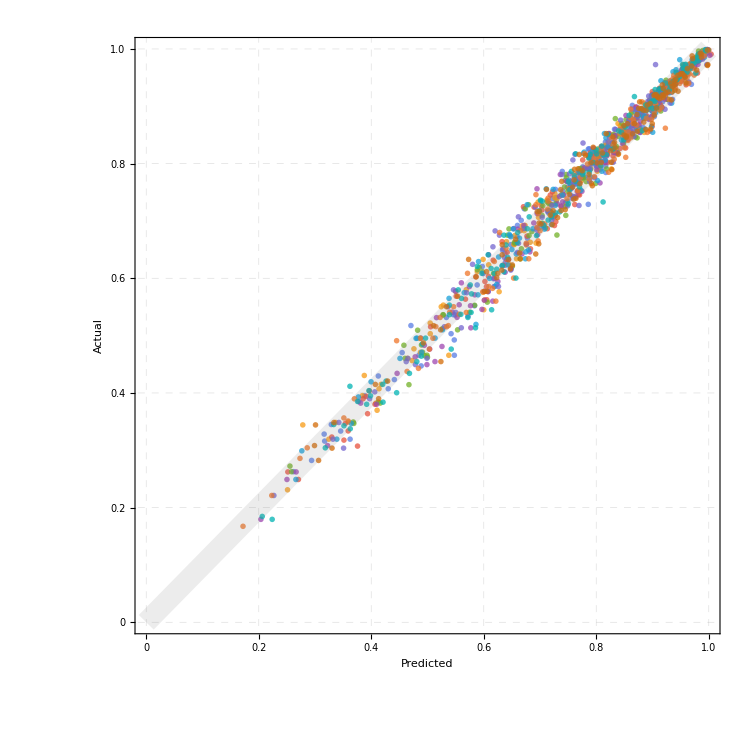

```mathematica
comparisonsPoints=Table[Flatten[trainPlots[[i,1,1,1,1,2,1,1,2,2]],1],{i,1,folds}];
ListPlot[comparisonsPoints
,AspectRatio->1
,Epilog->{Gray,Opacity[.15],Thickness[.02],Line[{{0,0},{1,1}}]}
,Frame->True
,FrameLabel->(Style[#,35]&/@{"Predicted","Actual"})
,FrameStyle->Directive[Gray,Thick]
,FrameTicksStyle->18
,GridLines->Automatic
,GridLinesStyle->Directive[Gray,Opacity[.25],Dashed,Thick]
,ImageSize->750
,PlotRange->{{0,1},{0,1}}
,PlotTheme->"Business"
,PlotStyle->Directive[Opacity[.75]]
]
```

Sensitivity Analysis

## Dropping Variables

```mathematica
pickedVariables={1,2,3,4};
{trainingPicked,validationPicked}=Table[
(#[[1]]->#[[2]])&/@Transpose[{
Transpose[i[[All,1,#]]&/@pickedVariables],
i[[All,2]]
}]
,{i,{training,validation}}];
```

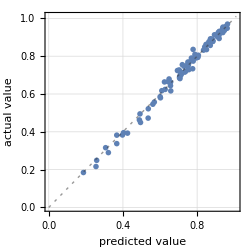
Predictor information
Input type | NumericalVector (length: 4)
Method | GradientBoostedTrees
Standard deviation | 0.0366 ± 0.0075
Loss | 0 ± 0.13
Single evaluation time | 3.38 ms/example
Batch evaluation speed | 55.5 examples/ms
Predictor memory | 686. kB
Training examples used | 864 examples
Training time | 8.44 s
 |  | Predictor Measurements
Number of test examples | 96
Standard deviation | 0.0191 ± 0.0017
Standard deviation baseline | 0.193 ± 0.015
Mean cross entropy | -2.43 ± 0.17
Single evaluation time | 3.53 ms/example
Batch evaluation speed | 2.59 examples/ms
-Graphics- |

```mathematica
predictionFunction=Predict[trainingPicked
,Method->"GradientBoostedTrees"
,PerformanceGoal->"Quality"
,TrainingProgressReporting->"SimplePanel"
,ValidationSet->validationPicked
];
Grid[{{
PredictorInformation[predictionFunction],
PredictorMeasurements[predictionFunction,validationPicked, "Report"]
}}]
```

## Gradient Calculation

```mathematica
Table[
vectorA={i,0,0,0.5};
vectorB={i+.05,0,0,0.5};
(**)
pointA=predictionFunction[vectorA];
pointB=predictionFunction[vectorB];
(**)
differenceVector=vectorB-vectorA;
differencePrediction=pointB-pointA;
(**)
{differenceVector->differencePrediction}
,{i,.65,.95,.01}]
```

{{{0.05,0,0,0.}→0.0159187},{{0.05,0,0,0.}→0.0159187},{{0.05,0,0,0.}→0.0159187},{{0.05,0,0,0.}→0.0115876},{{0.05,0,0,0.}→0.0115876},{{0.05,0,0,0.}→0.0115876},{{0.05,0,0,0.}→0.0115876},{{0.05,0,0,0.}→0.0267609},{{0.05,0,0,0.}→0.0151734},{{0.05,0,0,0.}→0.0151734},{{0.05,0,0,0.}→0.0151734},{{0.05,0,0,0.}→0.0151734},{{0.05,0,0,0.}→0.},{{0.05,0,0,0.}→0.},{{0.05,0,0,0.}→0.},{{0.05,0,0,0.}→0.0215593},{{0.05,0,0,0.}→0.0215593},{{0.05,0,0,0.}→0.0215593},{{0.05,0,0,0.}→0.0215593},{{0.05,0,0,0.}→0.0215593},{{0.05,0,0,0.}→0.},{{0.05,0,0,0.}→0.},{{0.05,0,0,0.}→0.},{{0.05,0,0,0.}→0.},{{0.05,0,0,0.}→0.},{{0.05,0,0,0.}→0.},{{0.05,0,0,0.}→0.},{{0.05,0,0,0.}→0.},{{0.05,0,0,0.}→0.},{{0.05,0,0,0.}→0.},{{0.05,0,0,0.}→0.}}